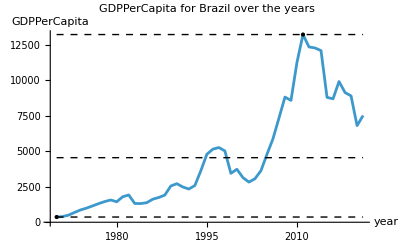

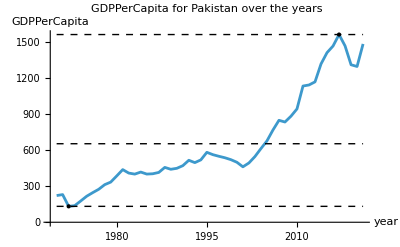

```mathematica
propPlot[country_,property_]:=Module[{Question1,dataQuestion1,cleanedDataQ1,valuesQ1,averagevalues,maximumvalues,minimumvalues,maximumpoint,minimumpoint,xAXISminimum,xAXISmaximum},
Question1=CountryData[country,{property,All}];
dataQuestion1=Normal[Question1["Path"]];
cleanedDataQ1=Map[{DateValue[#[[1]],"Year"],QuantityMagnitude[#[[2]]]}&,dataQuestion1];
cleanedDataQ1=Select[cleanedDataQ1,NumberQ[Last[#]]&&1960<=First[#]<=2022&];
valuesQ1=cleanedDataQ1[[All,2]];
averagevalues=Mean[valuesQ1];
maximumvalues=Max[valuesQ1];
minimumvalues=Min[valuesQ1];
maximumpoint=SortBy[cleanedDataQ1,Last][[-1]];
minimumpoint=SortBy[cleanedDataQ1,Last][[1]];
xAXISminimum=Min[cleanedDataQ1[[All,1]]];
xAXISmaximum=Max[cleanedDataQ1[[All,1]]];

plotLines={{Thick,Dashed,InfiniteLine[{0,averagevalues},{1,0}]},{Thin,Dashed,InfiniteLine[{0,maximumvalues},{1,0}]},{Thin,Dashed,InfiniteLine[{0,minimumvalues},{1,0}]},{Black,PointSize[Large],Point[{maximumpoint,minimumpoint}]}};

ListLinePlot[cleanedDataQ1,PlotLabel->property<>" for "<>country<>" over the years",AxesLabel->{"year",property},Epilog->{{Thick,Dashed,Line[{{xAXISminimum,averagevalues},{xAXISmaximum,averagevalues}}]},{Thin,Dashed,Line[{{xAXISminimum,maximumvalues},{xAXISmaximum,maximumvalues}}]},{Thin,Dashed,Line[{{xAXISminimum,minimumvalues},{xAXISmaximum,minimumvalues}}]},{Black,PointSize[Large],Point[maximumpoint]},{Black,PointSize[Large],Point[minimumpoint]}}]]

(*Testing Functions*)
propPlot["Brazil","GDPPerCapita"]
propPlot["Pakistan","GDPPerCapita"]
```